```mathematica
polarMap[func_,radial_,polar_,options___]:=ParametricPlot[Evaluate[Through[{Re,Im}[func]]],radial,polar,options];
cartesianMap[func_,xrange_,yrange_,options___]:=ParametricPlot[Evaluate[Through[{Re,Im}[func]]],xrange,yrange,options];
```

```mathematica
polarConformal[func_,radial_,polar_,options___]:=Show[GraphicsGrid[{{polarMap[r Exp[I t],radial,polar,options, DisplayFunction->Identity],polarMap[func,radial,polar,options,DisplayFunction->Identity]}},{}],DisplayFunction -> $DisplayFunction]
cartesianConformal[func_,xrange_,yrange_,options___]:=Show[GraphicsGrid[{{cartesianMap[x+I*y,xrange,yrange,options, DisplayFunction->Identity],cartesianMap[func,xrange,yrange,options,DisplayFunction->Identity]}},{}],DisplayFunction -> $DisplayFunction]
```

Ejemplo 11. Función  .

z^2

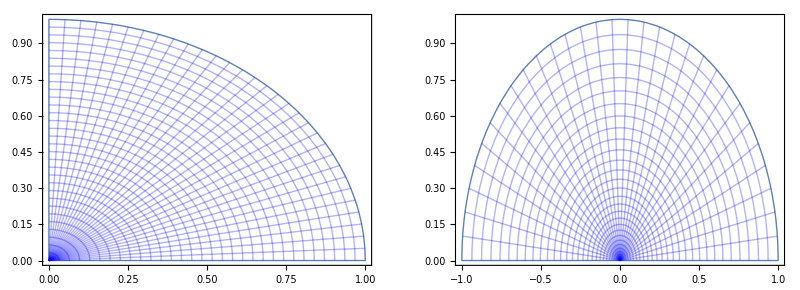

```mathematica
f1[z_]=z^2
polarConformal[f1[r Exp[I*t]],{r,0,1},{t,0,Pi/2},Mesh->{30,30},PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

z^3

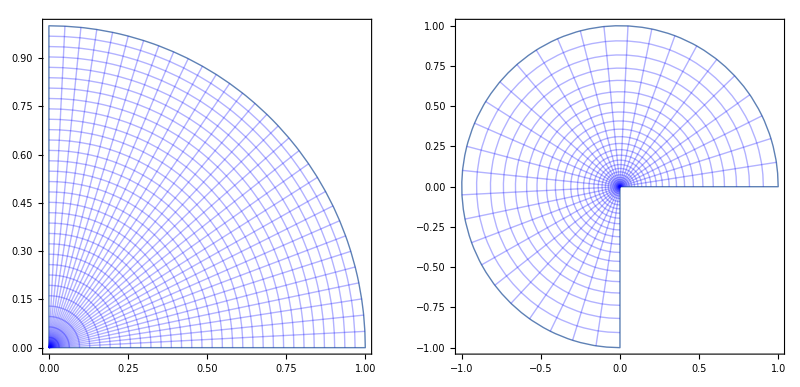

```mathematica
f2[z_]=z^3
polarConformal[f2[r Exp[I*t]],{r,0,1},{t,0,Pi/2},Mesh->{30,30},PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

z^4

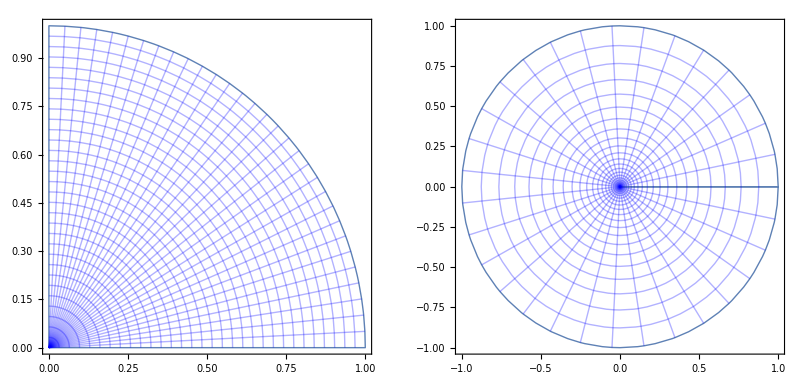

```mathematica
f3[z_]=z^4
polarConformal[f3[r Exp[I*t]],{r,0,1},{t,0,Pi/2},Mesh->{30,30},PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

La función

z^2

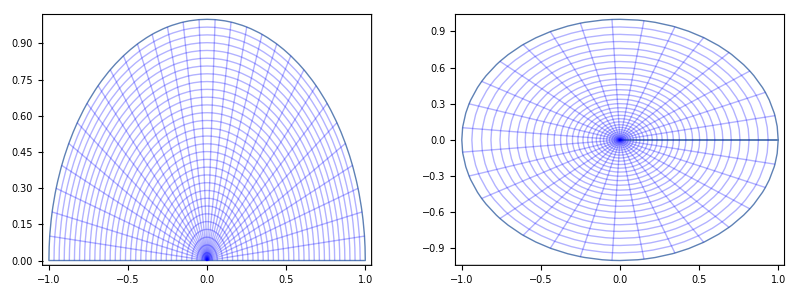

```mathematica
f5[z_]= z^2
polarConformal[f5[r Exp[I t]],{r,0,1},{t,0,Pi},Mesh->{30,30},PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

La función

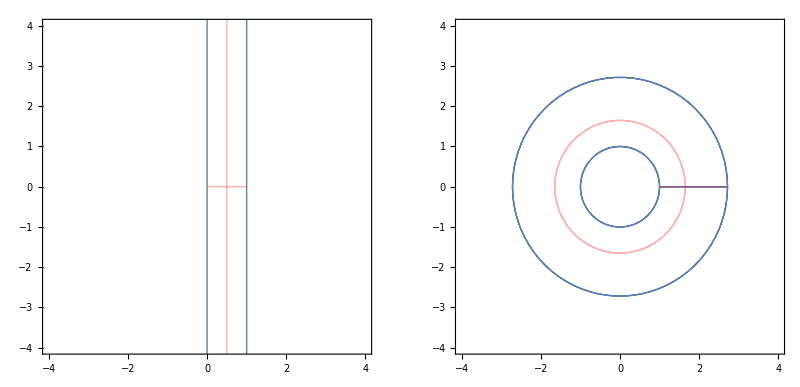

```mathematica
ClearAll[f,x,y,z]
f[z_] := Exp[z]
cartesianConformal[f[(x+I*y)],{x,0,1},{y,-2*Pi,2*Pi},Mesh->1,PlotRange->{{-4,4},{-4,4}},LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Red,Axes->True,PlotPoints->40]
```

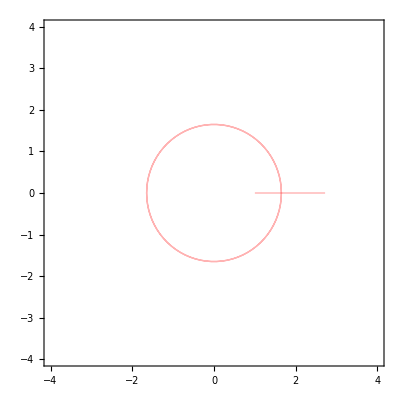

-Graphics-

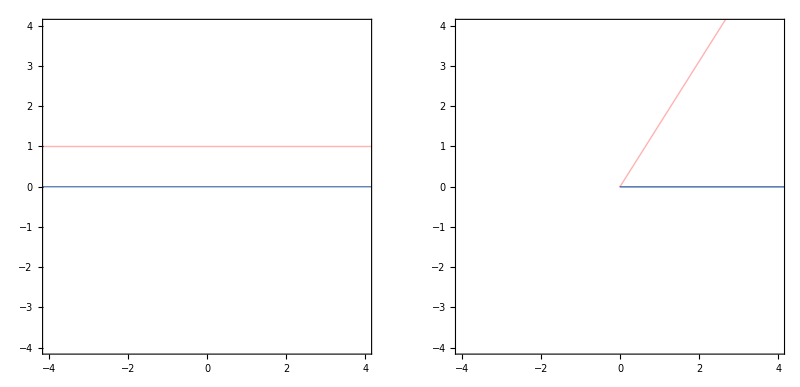

```mathematica
ClearAll[f6,x,y,z]
f6[z_]:= Exp[z]
cartesianConformal[f6[(x+I*y)],{x,-10,10},{y,0,2*Pi},Mesh->{{10},{1}},PlotRange->{{-4,4},{-4,4}},LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Red,Axes->True,PlotPoints->40]
```

ⅇ^z

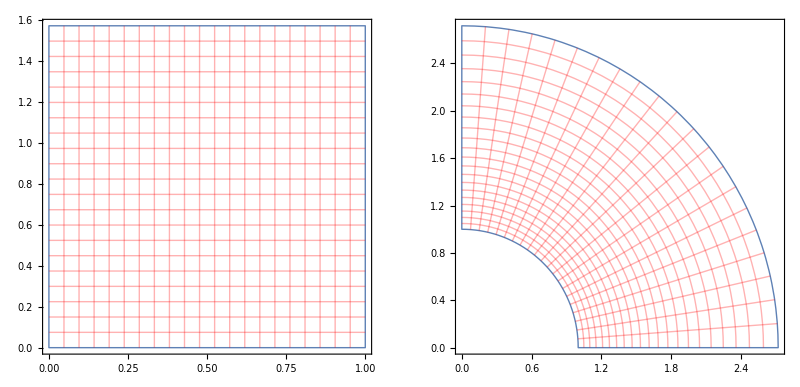

```mathematica
ClearAll[f,z,x,y]
f[z_] = Exp[z]
cartesianConformal[f[(x+I*y)],{x,0,1},{y,0,Pi/2},Mesh->20,PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Red,Axes->True,PlotPoints->40]
```

ⅇ^z

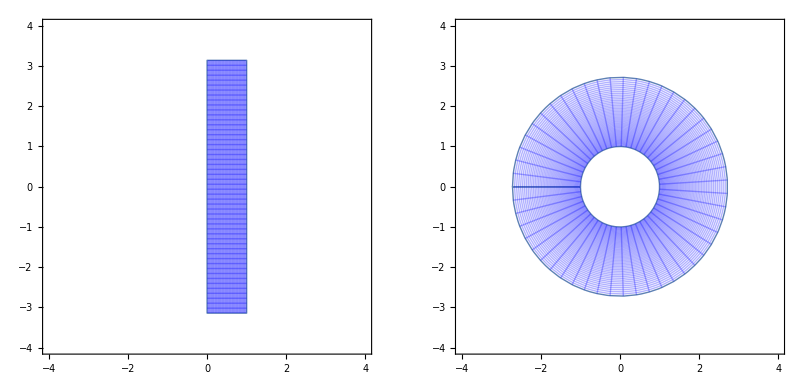

```mathematica
ClearAll[f,z,x,y]
f[z_] = Exp[z]
cartesianConformal[f[(x+I*y)],{x,0,1},{y,-Pi,Pi},Mesh->50,PlotRange->{{-4,4},{-4,4}},LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True,PlotPoints->40]
```

La función

```mathematica
ClearAll[f,z]
```

Log[z]

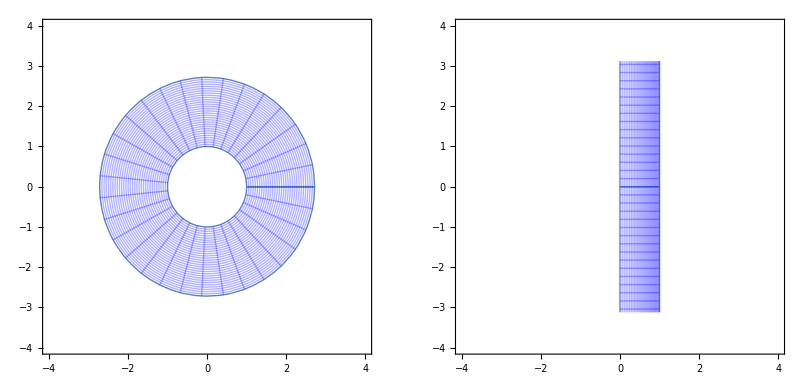

```mathematica
f[z_]= Log[z]
polarConformal[f[r Exp[I t]],{r,1,Exp[1]},{t,0,2*Pi},Mesh->{30,30},PlotRange->{{-4,4},{-4,4}},LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

## Transformaciones de Möbius

Proposición 6. La composición de dos transformaciones de Möbius es una transformación
de Möbius.

```mathematica
ClearAll[T,S,a,z,b,c,d,e,f,k,l]
T[z_] = (a z + b)/(c z + d);
S[z_] = (e z + f)/(k z + l);
```

```mathematica
Simplify[T[S[z]]]
```

(a f+b l+a e z+b k z)/(c f+d l+c e z+d k z)

```mathematica
Collect[Numerator[TS],z]/Collect[Denominator[%], z]
```

(a f+b l+(a e+b k) z)/(c f+d l+(c e+d k) z)

Proposición 7. El conjunto de transformaciones de Möbius con la composición de
funciones forman un grupo.

Asociatividad

```mathematica
ClearAll[T,S,a,z,b,c,d,e,f,k,l,m,n,q,r,R,TS,Id,T1,w]
T[z_] = (a z + b)/(c z + d);
S[z_] = (e z + f)/(k z + l);
R[z_] = (m z + n)/(q z + r);
```

```mathematica
Simplify[T[S[z]]]
```

(a f+b l+a e z+b k z)/(c f+d l+c e z+d k z)

```mathematica
TS[z_]=(a f+b l+a e z+b k z)/(c f+d l+c e z+d k z)
```

(a f+b l+a e z+b k z)/(c f+d l+c e z+d k z)

```mathematica
Simplify[TS[R[z]]];
Collect[Numerator[ %], z]/Collect[Denominator[ %], z]
```

(a e n+b k n+a f r+b l r+(a e m+b k m+a f q+b l q) z)/(c e n+d k n+c f r+d l r+(c e m+d k m+c f q+d l q) z)

```mathematica
SR[z_]=(e n+f r+e m z+f q z)/(k n+l r+k m z+l q z)
```

(e n+f r+e m z+f q z)/(k n+l r+k m z+l q z)

```mathematica
Simplify[T[SR[z]]];
Collect[Numerator[ %], z]/Collect[Denominator[ %], z]
```

(a e n+b k n+a f r+b l r+(a e m+b k m+a f q+b l q) z)/(c e n+d k n+c f r+d l r+(c e m+d k m+c f q+d l q) z)

Neutro

```mathematica
Id[z_] = z;
```

```mathematica
Simplify[Id[T[z]]]
```

(b+a z)/(d+c z)

```mathematica
Simplify[T[Id[z]]]
```

(b+a z)/(d+c z)

Inverso

```mathematica
T1[w_]:=(-b+d*w)/(a-c*w)
T1[w]
```

(-b+d w)/(a-c w)

```mathematica
Simplify[T[T1[w]]]
```

w

```mathematica
Simplify[T1[T[z]]]
```

z

Ejemplo 14

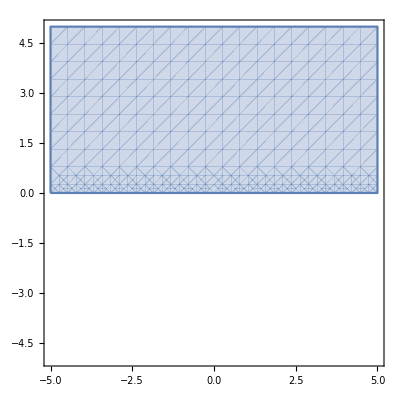

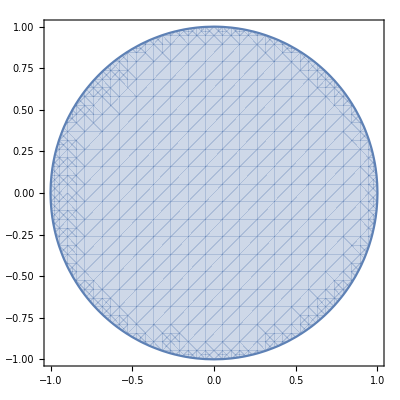

```mathematica
omega1 = ComplexRegionPlot[Im[z] >= 0, {z, -5 - 5I, 5 + 5I}]
omega2 = ComplexRegionPlot[Im[I*((1-w)/(w+1))] >= 0, {w, -1 - I, 1 + I}]
```

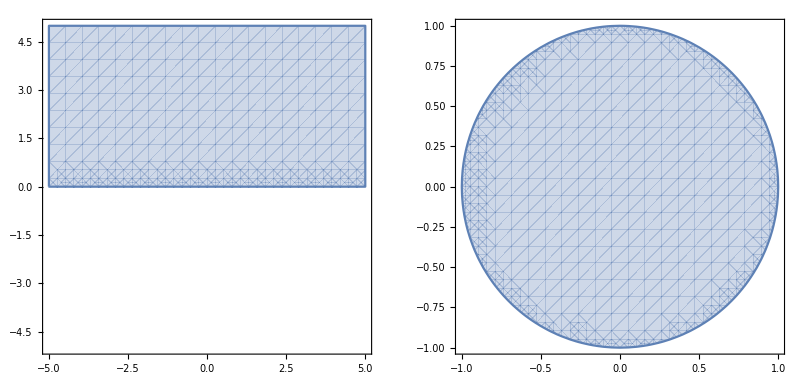

```mathematica
Show[GraphicsGrid[{{Graphics[omega1], Graphics[omega2]}},{}]]
```

```mathematica
ClearAll[z,f];
f[z_]=(I-z)/(z+I)
cartesianConformal[f[(x+I*y)],{x,-5,5},{y,0,5},Mesh->300,PlotRange->All,LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True,PlotPoints->40]
```

(ⅈ-z)/(ⅈ+z)

-Graphics-

```mathematica
ClearAll[w,z]
w[z_]= I*((1-z)/(z+1))
polarConformal[w[r Exp[I t]],{r,0,1},{t,0,2*Pi},Mesh->{300,300},PlotRange->{{-1,1},{-1,1}},LabelStyle->Directive[Larger,Bold],PlotStyle->White,MeshStyle->Blue,Axes->True]
```

(ⅈ (1-z))/(1+z)

-Graphics-

Ejemplo 15
1) si ,
2) si  ,
3) si ,
4) si  si  ,
5) si